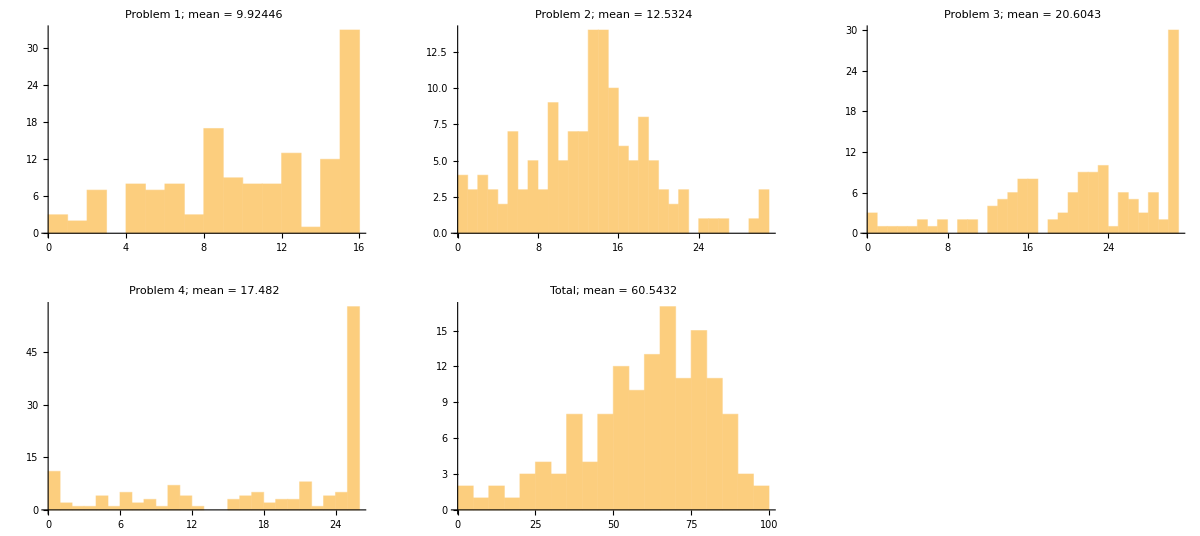

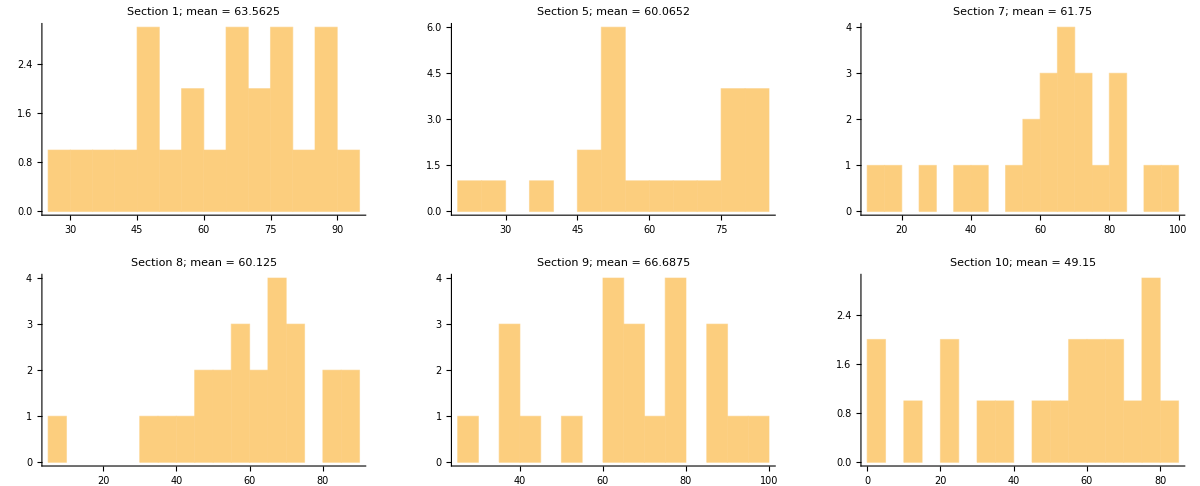

```mathematica
(*GradeReport.nb revision 05/10/2016. Written and maintained by Charles Hussong chussong@jhu.edu. Find most recent version at github.com/chussong/teaching-tools/*)

(*Takes grade data in a spreadsheet and outputs histograms of students' performance on each problem and on the overall exam. Expected data format is: names in first two columns, then each student's section number in third column, then each problem's score in subsequent columns. The top row is expected to be used for column labels and is not read.*)

(*Students whose problem scores are all blank will be treated as bad data and removed. Students whose scores are partially blank will have the blanks changed to 0s. No other data alterations are made.*)

ClearAll["Global`*"];
students=174; (*number of students with rows, including blank rows*)
maxpoints={15,30,30,25};  (*maximum points for each problem*)
totalBinSize=5; (*bin size for total-score histogram*)
dataname="mid1grades.xlsx";
exportName="mid1report.pdf";
SetDirectory["~/Dropbox/Classes/171.102/1617F/Data"];

(*--------------------------------------------------------------------------*)

(*Data reading and cleanup*)
problems=Length@maxpoints;
maxpoints=Append[Total@maxpoints]@maxpoints;
blankCondition={_,_,_};
Do[blankCondition=Append[""]@blankCondition,problems];
hist=ConstantArray[0,problems+1];
data=Import[dataname,"Data"];
If[Length@data==1,data=data[[1]]];
data=Take[data,{2,students+1}];
Do[data[[i]]=Take[data[[i]],{1,problems+3}],{i,1,students}];
students-=Length[Cases[blankCondition]@data];
data=DeleteCases[blankCondition]@data;
data=Replace[data,""->0,∞];
Do[data[[i]]=Append[Total@Take[data[[i]],{4,problems+3}]]@data[[i]],{i,1,students}];

(*Whole-class analysis and visualization*)
classMean=Mean@data[[All,problems+4]];
classMean=N[classMean,IntegerLength@Round@classMean+2];
classStDev=StandardDeviation@data[[All,problems+4]];
classStDev=N[classStDev,IntegerLength@Round@classStDev+2];
classMedian=Median@data[[All,problems+4]];
maxCount=ConstantArray[0,problems+1];
Do[maxCount[[i]]=Max@BinCounts[data[[All,3+i]],1];,{i,1,problems}];
maxCount[[problems+1]]=Max@BinCounts[data[[All,4+problems]],totalBinSize];
Do[
hist[[i]]=Histogram[data[[All,3+i]],{0,maxpoints[[i]]+1,1},PlotLabel->"Problem "<>ToString[i]<>"; mean = "<>ToString@N[Mean@data[[All,3+i]],4],AxesOrigin->0,PlotRange->Max@maxCount];
,{i,1,problems}]
totalEndpoint=maxpoints[[problems+1]]-Mod[maxpoints[[problems+1]],totalBinSize];
hist[[problems+1]]=Histogram[data[[All,problems+4]],{0,totalEndpoint+1,totalBinSize},PlotLabel->"Total; mean = "<>ToString@N[Mean@data[[All,4 + problems]],4],AxesOrigin->0,PlotRange-> Max@maxCount];
columns=Ceiling@Sqrt@(problems+1);
rows=Ceiling@((problems+1)/columns);
histGrid=ConstantArray["",{rows,columns}];
pos={1,1};
Do[histGrid[[pos[[1]],pos[[2]]]]=hist[[i]];
pos[[2]]++;
If[pos[[2]]>columns,
pos[[1]]++;
pos[[2]]=1;
];
,{i,1,problems+1}];
Print[GraphicsGrid[histGrid,ImageSize->Full]];

(*Section analysis and visualization*)
highestSection=Round@Max@data[[All,3]];
If[highestSection>0,
secData=Table[{},highestSection];secHist=ConstantArray[0,highestSection];
sectionMeans=ConstantArray[0,highestSection];
sectionMaxCount=ConstantArray[0,highestSection];
scoreVectors=data[[All,Range[3,problems+4]]];
Do[If[scoreVectors[[row]][[1]]>0,
secData[[scoreVectors[[row]][[1]]]]=Append[secData[[scoreVectors[[row]][[1]]]],scoreVectors[[row]][[Range[2,problems+2]]]];
];
,{row,1,students}];
Do[sectionMaxCount[[i]]=Max@BinCounts[secData[[i]][[All,problems+1]],totalBinSize];,{i,1,highestSection}];
Do[If[sectionMaxCount[[i]]==0,Continue[]];
sectionMeans[[i]]=Mean@secData[[i]][[All,problems+1]];
sectionMeans[[i]]=N[sectionMeans[[i]],IntegerLength@Round@sectionMeans[[i]]+2];
secHist[[i]]=Histogram[secData[[i]][[All,problems+1]],{0,totalEndpoint,totalBinSize},PlotRange->Max@sectionMaxCount,PlotLabel-> "Section "<>ToString[i]<>"; mean = "<>ToString[sectionMeans[[i]]]];
,{i,1,highestSection}];
secColumns=Ceiling@Sqrt@(highestSection-Count[sectionMaxCount,0]);
secRows=Ceiling@((highestSection-Count[sectionMaxCount,0])/secColumns);
secHistGrid=ConstantArray["",{secRows,secColumns}];
pos={1,1};
Do[If[sectionMaxCount[[i]]==0,Continue[]];
secHistGrid[[pos[[1]],pos[[2]]]]=secHist[[i]];
pos[[2]]++;
If[pos[[2]]>secColumns,
pos[[1]]++;
pos[[2]]=1;
];
,{i,1,highestSection}];
Print[GraphicsGrid[secHistGrid,ImageSize->Full]];
];

(*Create and export PDF report*)
report=CreateDocument[];
SetOptions[report,PageHeaders->{{None,None,None},{None,None,None}},PageFooters->{{None,None,None},{None,None,None}},PrintingOptions->{"PaperOrientation"->"Landscape","PrintingMargins"->{{20,20},{40,40}}}];
Paste[report,GraphicsGrid[histGrid,ImageSize->Full]];Paste[report,Framed["Additional statistics:\t\t St.Dev. = "<>ToString@classStDev<>"\t\t median = "<>ToString@N[classMedian]]];
If[highestSection>0,Paste[report,GraphicsGrid[secHistGrid,ImageSize->Full]]];
Export[exportName,report];
NotebookClose[report];
```

```mathematica
data
```

{{AINSWORTH,MICHAEL,9.,15.,5.,30.,25.,75.},{ALEXANDER,ALICE,1.,6.,18.,22.,20.,66.},{BATES,HALEY,7.,9.,17.,14.,25.,65.},{BAZAN-BERGAMINO,EMMANUEL,10.,12.,8.,23.,25.,68.},{BHAT,VIPUL,9.,14.,26.,30.,25.,95.},{BROWN,MATTHEW,1.,4.,3.,16.,7.,30.},{BURRELL,AVERY,1.,4.,12.,12.,21.,49.},{CAGIR,REID,1.,6.,9.,5.,19.,39.},{CAI,XINYI,1.,15.,19.,30.,25.,89.},{CENTENO,KEVIN,10.,6.,3.,3.,1.,13.},{CHANG,ALEXANDER,8.,15.,18.,20.,21.,74.},{CHANG,CRYSTAL,8.,14.,16.,16.,25.,71.},{CHEN,SHUN WEN,7.,0.,9.,18.,10.,37.},{CHIAO,JIA YUEE,9.,11.,19.,30.,25.,85.},{CHOI,ALEX,10.,5.,12.,12.,9.,38.},{CHU,STANLEY,5.,9.,18.,30.,23.,80.},{COLOMBO,JENNA,1.,4.,12.,4.,8.,28.},{CORTES,ROBERT,1.,12.,5.,21.,10.,48.},{CRITTENDON III,KENNETH,1.,12.5,16.,16.,3.,47.5},{DE LA CRUZ,AVERY,1.,12.,16.,20.,7.,55.},{DISORBO,THOMAS,1.,8.5,9.,30.,25.,72.5},{DUMAN,CAROLYN,10.,15.,10.,30.,11.,66.},{ELANDER,ANNIE,7.,2.,9.,6.,11.,28.},{FERNANDES,GABRIEL,5.,15.,17.,22.,25.,79.},{FIGUEROA,JOSEPH,1.,15.,18.,16.,21.,70.},{FRAZIER,ANNA,9.,12.,19.,30.,25.,86.},{GARLOW,BENJAMIN,8.,9.,14.,21.,25.,69.},{GARZA,MATTHEW,5.,8.,2.,15.,25.,50.},{GAYEN,MAHASHWETA,5.,11.5,14.,14.,11.,50.5},{GEE,KAYLA,9.,10.,20.,19.,25.,74.},{GIRISH,AKANKSHA,5.,8.,5.,16.,0.,29.},{GLOVER,THOMAS,1.,14.5,22.,22.,25.,83.5},{GOLDSTEIN,ZOE,9.,4.,13.,13.,6.,36.},{GRIMMETT,MARIA,8.,2.,7.,10.,17.,36.},{GULINO,AVERY,9.,14.5,4.,28.,21.,67.5},{GULINO,MARIA,10.,15.,15.,25.,0.,55.},{GUNDRUM,JONAH,7.,10.,1.,19.,25.,55.},{GUNN,JONATHAN,7.,5.,12.,24.,25.,66.},{GUO,JOANNA,8.,9.,5.,30.,25.,69.},{GUO,MICHELLE,7.,8.,7.,14.,11.,40.},{GUO,RICHARD,9.,14.5,14.,25.,25.,78.5},{HERNANDEZ,IAN,1.,15.,16.,30.,25.,86.},{HOU,TIFFANY,8.,12.5,14.,13.,19.,58.5},{HOWARD,THOMAS,9.,15.,2.,26.,25.,68.},{JACOB,LAUREN,7.,8.,15.,25.,25.,73.},{JANG,JIHOON,8.,15.,18.,30.,25.,88.},{JOHN,JOHN,8.,6.5,15.,23.,25.,69.5},{JUKES,MARGARET,9.,14.5,9.,21.,16.,60.5},{KARKI,SABIN,8.,9.,9.,21.,21.,60.},{KEDIA,VARUN,9.,4.,6.,15.,15.,40.},{KERANS,SAMUEL,10.,12.,13.,27.,23.,75.},{KHIM,RYAN,10.,8.,13.,5.,25.,51.},{KIM,ESTHER,10.,9.,5.,9.,0.,23.},{KIM,HA EUN,10.,8.,10.,2.,4.,24.},{KOOK,MINJEE,9.,8.,7.,15.,6.,36.},{KOUL,ARMAN,1.,2.,17.,25.,25.,69.},{KUNG,YU JUI,9.,8.,13.,30.,10.,61.},{KUROKI,GRACE,7.,15.,11.,28.,17.,71.},{KWAN,EMILY,10.,12.,3.,23.,8.,46.},{LAMAS,RODRIGO,5.,8.,12.,14.,25.,59.},{LANGAN,LAWRENCE,10.,5.,14.,30.,25.,74.},{LAPINSKI,MAYA,10.,1.,15.,30.,17.,63.},{LEE,DONGWOO,9.,15.,30.,30.,25.,100.},{LEE,MICHELLE,7.,6.,0.,7.,6.,19.},{LEE,THEODORE,9.,11.,13.,19.,24.,67.},{LEVINE,MARC,10.,15.,14.,30.,17.,76.},{LIM,BRANDON,8.,15.,16.,18.,25.,74.},{LIU,EDWARD,9.,12.5,15.,22.,15.,64.5},{LU,DAYA,7.,4.,16.,26.,16.,62.},{LU,RYAN,9.,15.,11.,25.,25.,76.},{MAHERAS,EMILY,8.,15.,9.,23.,0.,47.},{MARTINEZ,NATALIE,5.,2.,10.,9.,2.,23.},{MATHEW,ELIZABETH,1.,1.,8.,15.,19.,43.},{MCCAFFERTY,CONNOR,8.,7.5,14.,13.,0.,34.5},{MCGAUGH,SCOTT,7.,15.,30.,27.,25.,97.},{MEURER,KATHERINE,8.,12.5,11.,16.,20.,59.5},{MILLER,GILLIAN,5.,2.,12.,21.,0.,35.},{MILLER,JONATHAN,8.,4.,6.,30.,12.,52.},{MONTOYA,ALLISON,1.,2.,14.,22.,25.,63.},{MORINA,LUKE,8.,10.,15.,30.,25.,80.},{MOYLAN,LIAM,7.,14.5,22.,21.,25.,82.5},{NAVARRO,DANTE,5.,15.,14.,29.,22.,80.},{NICO,ELSA,10.,15.,18.,20.,25.,78.},{NIXON,KRISTEN,9.,9.,1.,15.,25.,50.},{OGUNNAIKE,LAOLU,8.,5.,7.,30.,25.,67.},{OKEKE,CHIGOZIE,10.,4.,9.,14.,6.,33.},{OYENUSI,OLUWABUNMI,9.,11.,1.,20.,4.,36.},{PARK,JEYEON,5.,5.,15.,28.,0.,48.},{PARK,STEPHEN,1.,15.,13.,25.,23.,76.},{PARK,SUNG JAE,10.,0.,0.,0.,0.,0.},{PARKER,DANIEL,5.,8.,13.,30.,15.,66.},{PATEL,KISHA,1.,15.,20.,29.,24.,88.},{PATEL,KRISHNA,7.,15.,13.,16.,24.,68.},{PEREZ-ROLDAN,DANIELA,5.,8.,5.,21.,17.,51.},{PETERSEN,KRISTEN,8.,7.,4.,20.,25.,56.},{PITAKTONG,ISAREE,5.,12.,17.,30.,18.,77.},{QURESHI,ZAN,5.,15.,12.,28.,25.,80.},{RASTOGI,SHIVAM,1.,8.5,13.,30.,25.,76.5},{RAVEKES,JOHN,7.,11.5,0,0,0,11.5},{REDDY,MEENA,8.,6.,18.,14.,5.,43.},{RIVERA,PEDRO,8.,15.,30.,15.,25.,85.},{ROBERTS,JAMES,5.,15.,10.,28.,25.,78.},{ROBERTSON,BAILEY,9.,11.5,11.,7.,0.,29.5},{ROBINETTE,MICHAEL,1.,9.,21.,22.,25.,77.},{ROBINSON,LUCAS,5.,2.,14.,10.,25.,51.},{RODRIGUEZ,RODOLFO,1.,10.,11.,22.,16.,59.},{SANIEI,SAMI,5.,10.,10.,15.,25.,60.},{SANTURIAN,SIMON,5.,10.,6.,22.,10.,48.},{SEHGAL,SHUCHI,1.,8.,13.,28.,18.,67.},{SEVENSKY,RILEY,1.,14.5,15.,12.,10.,51.5},{SHAJIHAN,KAHMIL,7.,8.5,20.,30.,25.,83.5},{SHIN,SAMUEL,7.,6.,13.,12.,21.,52.},{SIORDIA,ISABEL,8.,5.,2.,1.,1.,9.},{SONMEZ,RUZGAR,9.,14.,14.,23.,25.,76.},{STATE,CLAIRE,7.,15.,15.,23.,10.,63.},{STRICKLAND,SOPHIA,8.,12.5,2.,23.,24.,61.5},{SU,MATTHEW,1.,15.,22.,30.,25.,92.},{SUMIBCAY,TYRONE JOHN,5.,11.,11.,27.,4.,53.},{TALUR,MEGHA,10.,0.,0.,0.,0.,0.},{THOMAS,SYDNEY,5.,15.,13.,26.,21.,75.},{THYAGARAJAN,ANISH,9.,14.,5.,21.,23.,63.},{TRAN LE,MINH-TAM,7.,11.,13.,23.,24.,71.},{TROYANO-VALLS,CLARA,7.,10.,14.,23.,8.,55.},{VAN CAUWELAERT DE WYELS,JASPER,7.,14.5,17.,30.,21.,82.5},{VILLAVISANIS,DILLAN,5.,5.,7.,22.,20.,54.},{WANG,KAIWEN,9.,15.,21.,30.,25.,91.},{WEN,BRONTE,5.,7.,29.,13.,25.,74.},{WEN,FANGJIA,7.,15.,19.,26.,16.,76.},{WOLFINGER,BRETT,9.,15.,15.,30.,25.,85.},{WU,LUCY,7.,15.,13.,13.,25.,66.},{XIAN,FENGFAN,8.,10.,14.,16.,10.,50.},{XIE,YANGYIRAN,7.,14.,25.,30.,25.,94.},{YANG,JEONGHEE,10.,6.,24.,21.,4.,55.},{YANG,TENG-JU,10.,9.,9.,20.,25.,63.},{YE,BURTON,7.,8.,8.,23.,25.,64.},{YE,WILLIAM,10.,8.,19.,30.,25.,82.},{YOO,SUN JAY,8.,13.5,14.,30.,25.,82.5},{YOUNGER,KALYN,8.,15.,11.,15.,6.,47.},{ZENG,SIMON,5.,12.,18.,26.,25.,81.}}